```mathematica
f[x_]:=Expand[x]
Plot[f[x],{x,-5,5}, AspectRatio->1]   (*Ésta es la gráfica de una función lineal, la función es de tipo polinomial, el dominio y el rango son todos los números reales, se intersecta en 'x' y 'y' en el origen, la función es impar y es simétrica con respecto al origen*)
```

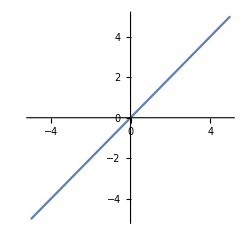

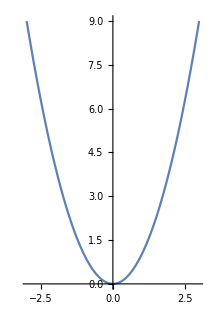
```mathematica
f[x_]:=Expand[x^2]
Plot[f[x],{x,-3,3},AspectRatio->Automatic]   (*Ésta es la gráfica de una función cuadrática, es de tipo polinomial y/o potencia, el dominio son todos los números reales, y el rango=[0,+INF], corta a 'x' y 'y' en el origen, la gráfica es par y simétrica con respecto al eje 'y' *)
-Graphics-
```

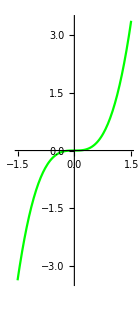
```mathematica
f[x_]:=Expand[x^3]
Plot[f[x],{x,-1.5,1.5},AspectRatio->Automatic, PlotStyle->Green] (*Ésta es la gráfica de una función cúbica, la cual es polinomial y/o potencia, el Dominio y Rango es R, la función es impar, es simétrica con respecto al origen, intersecta a 'x' y 'y' en el origen*)
-Graphics-
```

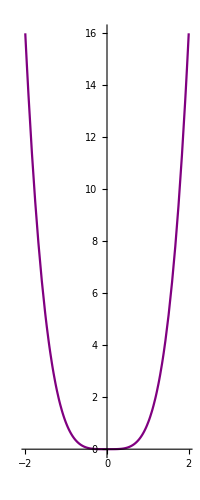

```mathematica
f[x_]:=Expand[x^4]
Plot[f[x],{x,-2,2}, AspectRatio->Automatic, PlotStyle->Purple]   (*Ésta es la gráfica de una función polinomial o potencia, donde el exponente de x es 4. El dominio son todos los número reales, y el rango está en el intervalo [0,+INF). Intersecta a 'x' y a 'y' en el origen, la función es par y simétrica con respecto al eje 'y' *)
```

```mathematica
f[x_]:=Expand[1/x]
Plot[f[x],{x,-5,5},AspectRatio->1,PlotStyle->Pink] (*Ésta es la gráfica de una función racional y/o potencia. El dominio de 'x' y 'y' son todos los reales menos el 0, la gráfica, no corta nunca al eje 'x' ni al eje 'y', la función no es par pero es impar, y es simétrica con respecto al origen*)
```

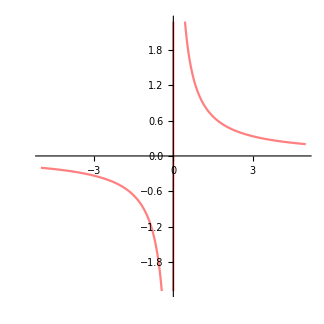

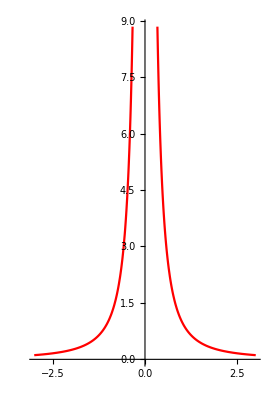

```mathematica
f[x_]:=Expand[1/(x^2)]
Plot[f[x],{x,-3,3}, AspectRatio->Automatic,PlotStyle->Red]   (*Ésta es la gráfica de una función potencia y/o racional. El dominio de x son todos los reales menos el cero y el rango es (0,+INF). La gráfica nunca va a intersectar a 'x' o a 'y'. La función es par y simétrica con respecto al eje 'y'*)
```

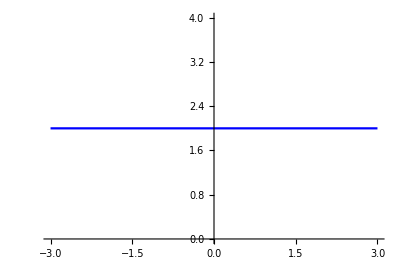

```mathematica
f[x_]:=Expand[2]
Plot[f[x], {x,-3,3},AspectRatio->Automatic, PlotStyle->Blue] (*Ésta es la gráfica de una función constante que sin importar el valor de 'x' y=2. El dominio son todos los reales y el rango es únicamente 2. La gráfica no cortará nunca al eje 'x' pero corta a 'y' en 2. Es una función par y la gráfica es simétrica con respecto al eje 'y'*)
```

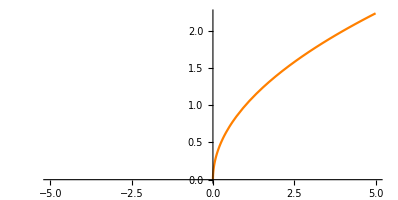

```mathematica
f[x_]:=Expand[Sqrt[x]]
Plot[f[x],{x,-5,5},AspectRatio->Automatic,PlotStyle->Orange]  (*La función es potencial, con exponente=1/2. El dominio y el rango es [0,+INF), pasa por el eje 'x' y el eje 'y' en el origen. No es par ni impar, por lo que no tiene ningun tipo de simetria *)
```

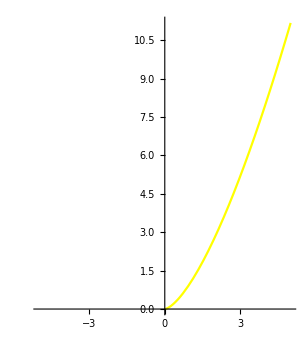

```mathematica
f[x_]:=Expand[Sqrt[x^3]]
Plot[f[x],{x,-5,5}, AspectRatio->Automatic,PlotStyle->Yellow]    (*La función es potencial, con exponente=3/2. El dominio y el rango es [0,+INF), pasa por el eje 'x' y el eje 'y' en el origen. No es par ni impar, por lo que no tiene ningun tipo de simetria *)
```

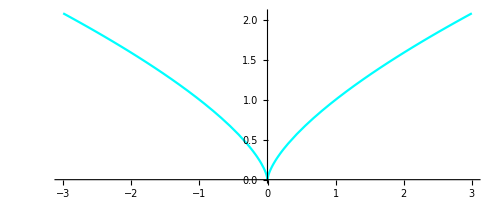

```mathematica
f[x_]:=Expand[CubeRoot[x^2]]
Plot[f[x],{x,-3,3},AspectRatio->Automatic, PlotStyle->Cyan]  (*La función es potencial, con exponente=2/3. El dominio es (-INF,+INF) y el rango es [0,+INF), pasa por el eje 'x' y el eje 'y' en el origen. Es par, por lo que tiene simetria con respecto a 'y'*)
```

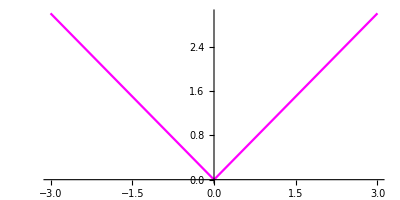

```mathematica
f[x_]:=Expand[Abs[x]]
Plot[f[x],{x,-3,3},AspectRatio->Automatic,PlotStyle->Magenta]   (*Esta es la grafica de una funcion valor abosoluto. El dominio son todos los numeros reales, y el rango es[0,+INF). La funcion es par por lo tanto es simetrica con respecto al eje 'y'*)
```

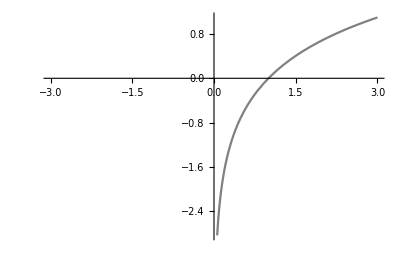

```mathematica
f[x_]:=Expand[Log[x]]
Plot[f[x],{x,-3,3},AspectRatio->Automatic,PlotStyle->Gray]  (*Esta es la grafica de una funcion logaritmica. El dominio es (0,+INF), y el rango es[-INF,+INF). La funcion no corta al eje 'y', pero corta a x en 1. La funcion no es par ni impar por lo tanto no tiene simetria*)
```

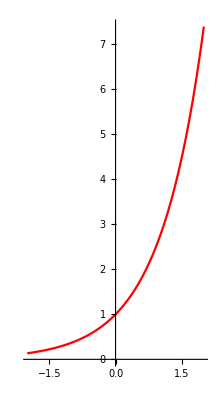

```mathematica
f[x_]:=Expand[Exp[x]]
Plot[f[x], {x,-2,2},AspectRatio->Automatic, PlotStyle->Red]  (*Esta es la grafica de una funcion exponencial. El dominio es (-INF,+INF), y el rango es (0,+INF). La funcion no corta al eje 'x', pero corta a 'y' en 1. La funcion no es par ni impar por lo tanto no tiene simetria*)
```

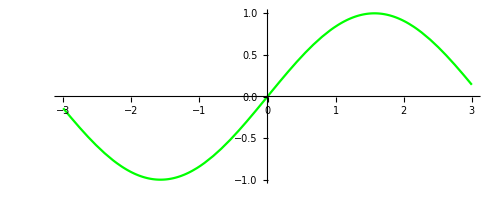

```mathematica
f[x_]:=Expand[Sin[x]]
Plot[f[x],{x,-3,3},AspectRatio->Automatic, PlotStyle->Green] (*Esta es la grafica de la funcion Seno. El dominio es (-INF,+INF), y el rango es [-1,1]. La funcion corta al eje 'x' en nπ siendo n un entero o cero(muchas veces), y a 'y' en el origen. La funcion es impar por lo tanto tiene simetria con respecto al origen*)
```

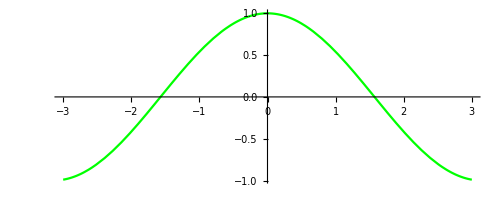

```mathematica
f[x_]:=Expand[Cos[x]]
Plot[f[x], {x,-3,3},AspectRatio->Automatic,PlotStyle->Green]    (*Esta es la grafica de la funcion Coseno. El dominio es (-INF,+INF), y el rango es [-1,1]. La funcion corta al eje 'x' en π/2+nπ siendo n un entero o '0'(muchas veces), y a'y' en el punto(0,1). La funcion es par por lo tanto tiene simetria con respecto al eje 'y'*)
```

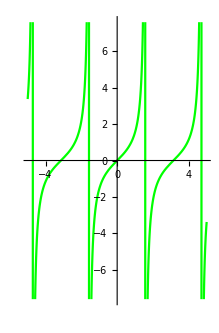

```mathematica
f[x_]:=Expand[Tan[x]]
Plot[f[x],{x,-5,5}, AspectRatio->Automatic, PlotStyle->Green]   (*Esta es la grafica de la funcion Tangente. El dominio es R-{multiplos impares de π/2}, y el rango es R. Corta a 'x' en nπ siendo n un entero o el '0', y corta a 'y' en el origen. No es par ni impar as[i que no tiene simetria *)
```

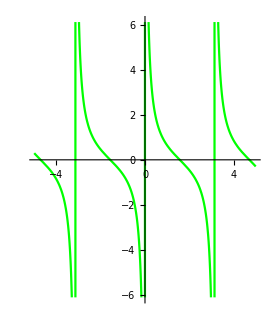

```mathematica
f[x_]:=Expand[Cot[x]]
Plot[f[x],{x,-5,5},AspectRatio->Automatic, PlotStyle->Green]   (*Esta es la grafica de la funcion Cotangente. El dominio es R-{multiplos de π}, y el rango es R. Corta a 'x' en nπ/2 siendo n un entero impar, y nunca corta a 'y'. No es par ni impar asi que no tiene simetria *)
```

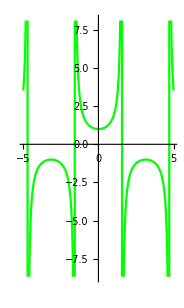

```mathematica
f[x_]:=Expand[Sec[x]]
Plot[f[x],{x,-5,5},AspectRatio->Automatic, PlotStyle->Green] (*Esta es la grafica de la funcion Secante. El dominio es R-{π/2+nπ siendo n un entero o el '0'}, y el rango es (-INF,-1]U[1,INF). Nunca corta a 'x', y corta a 'y' en (0,1). Es par asi que tiene simetria con respecto al eje 'y' *)
```

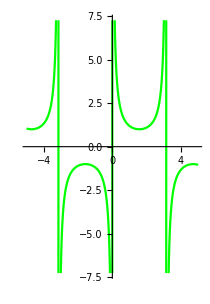

```mathematica
f[x_]:=Expand[Csc[x]]
Plot[f[x],{x,-5,5},AspectRatio->Automatic, PlotStyle->Green]   (*Esta es la grafica de la funcion Cosecante. El dominio es R-{nπ siendo n un entero o el '0'}, y el rango es (-INF,-1]U[1,INF). Nunca corta a 'x', y tampoco corta a 'y'. Es impar asi que tiene simetria con respecto al origen *)
```

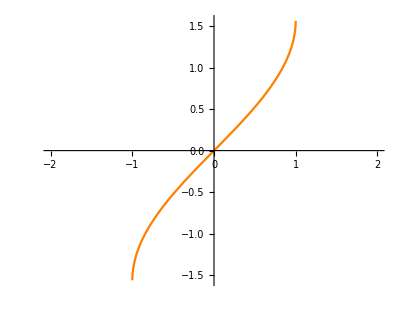

```mathematica
f[x_]:=Expand[ArcSin[x]]
Plot[f[x],{x,-2,2},AspectRatio->Automatic,PlotStyle->Orange]  (*Esta es la grafica de la funcion Arcoseno. El dominio es [-1,1] y el rango[-π/2,π/2]. Corta a 'x' y a 'y' en el origen. Es impar asi que tiene simetria con respecto al origen *)
```

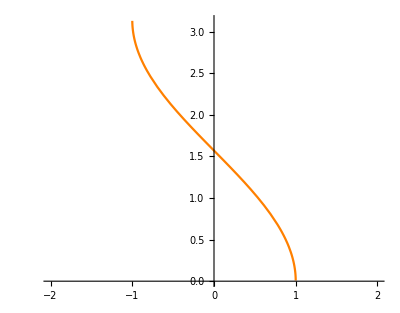

```mathematica
f[x_]:=Expand[ArcCos[x]]
Plot[f[x],{x,-2,2},AspectRatio->Automatic,PlotStyle->Orange](*Esta es la grafica de la funcion Arcoseno. El dominio es [-1,1] y el rango[0,π]. Corta a 'x' en (1,0) y a 'y' en (0,π/2). No es par ni impar asi que no tiene simetria *)
```

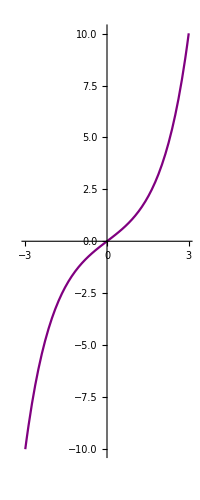

```mathematica
f[x_]:=Expand[Sinh[x]]
Plot[f[x],{x,-3,3},AspectRatio->Automatic, PlotStyle->Purple] (*Esta es la grafica de la funcion Seno hiperbolico. El dominio y el rango son todos los reales. Corta a 'x' y a 'y' en el origen. Es impar asi que tiene simetria con respecto al origen *)
```

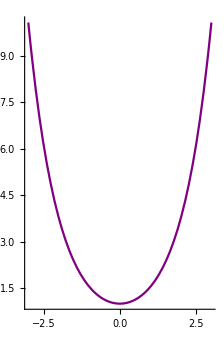

```mathematica
f[x_]:=Expand[Cosh[x]]
Plot[f[x],{x,-3,3},AspectRatio->Automatic, PlotStyle->Purple]  (*Esta es la grafica de la funcion Coseno hiperbolico. El dominio son todos los reales y el rango es [1,+INF). No corta a 'x', y corta a 'y' en (0,1). Es par asi que tiene simetria con respecto al eje 'y' *)
```

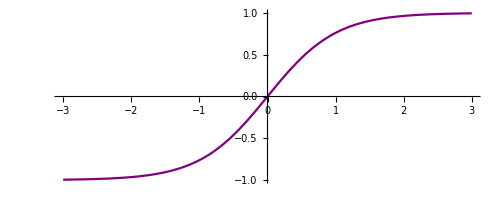

```mathematica
f[x_]:=Expand[Tanh[x]]
Plot[f[x],{x,-3,3}, AspectRatio->Automatic, PlotStyle->Purple]   (*Esta es la grafica de la funcion Tangente hiperbolica. El dominio son todos los reales, y el rango es (-1,1). Corta a 'x' y a 'y' en el origen. Es impar asi que tiene simetria con respecto al origen *)
```

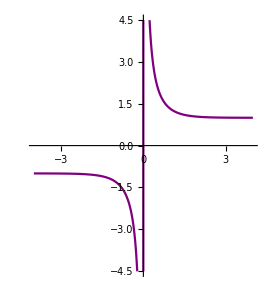

```mathematica
f[x_]:=Expand[Coth[x]]
Plot[f[x],{x,-4,4}, AspectRatio->Automatic, PlotStyle->Purple] (*Esta es la grafica de la funcion Cotangente Hiperbolica. El dominio es (-INF,0)U(0,INF), y el rango es (-INF,-1)U(1,+INF). La funcion no corta al eje 'x' ni al 'y'. La funcion es impar por lo tanto tiene simetria con respecto al origen*)
```

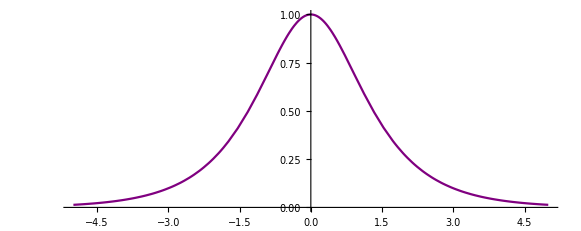

```mathematica
f[x_]:=Expand[Sech[x]]
Plot[f[x],{x,-5,5}, AspectRatio->Automatic, PlotStyle->Purple]  (*Esta es la grafica de la funcion Secante Hiperbolica. El dominio es R, y el rango es (0,1). No corta a 'x' y el corte con 'y' es indeterminado. Es par asi que tiene simetria con respecto al eje 'y' *)
```

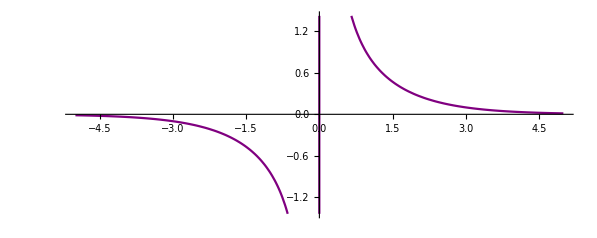

```mathematica
f[x_]:=Expand[Csch[x]]
Plot[f[x], {x,-5,5}, AspectRatio->Automatic, PlotStyle->Purple]   
(*Esta es la grafica de la funcion Cosecante Hiperbolica. El dominio y el rango es R-{0}. No corta a 'x' ni a 'y'. Es impar asi que tiene simetria con respecto al origen *)
```